NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

NDSolve completed. Solution validity: SUCCESS

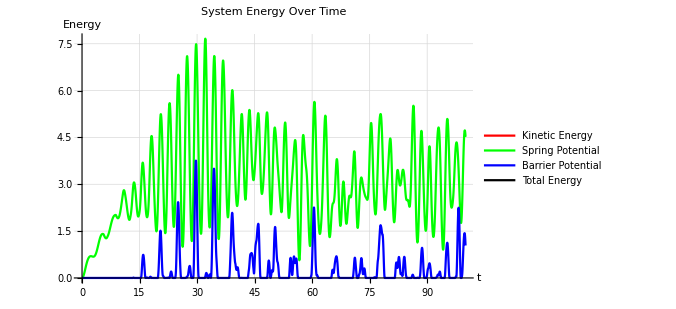

-Graphics3D-

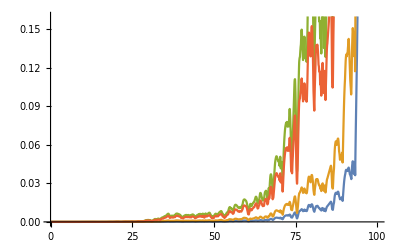

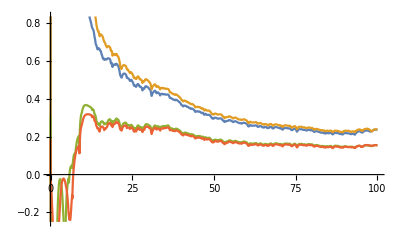

```mathematica
(*Transient Motion Simulation of a 1D Atomic Chain in 2D Space with Linear Restoring Force*)ClearAll["Global`*"];

(*Parameter Settings*)
nAtoms=10;(*Number of atoms*)
m=1;(*Mass of each atom*)
a=1;(*Lattice constant*)
k1x=1;(*Spring constant between atoms*)
k1y=1;(*Spring constant between atoms*)
k2=0;
k3=2;(*Elastic constant of the barrier (restoring force strength)*)
γ=0;
y0=1;(*Barrier equilibrium position*)
tMax=100;(*Total simulation time*)
Subscript[A, x]=0.1;Subscript[A, y]=1;
ω=1;
(*Initial conditions*)
initialVelocities=Table[{0.0,0.0},{n,nAtoms}];
xEq[n_]:=n*a;yEq[n_]:=0;
(*Initial conditions purterbation*)
initialVelocities2=initialVelocities;
initialVelocities2[[5,2]]=0.0000001;
initialVelocities3=initialVelocities;
initialVelocities3[[8,2]]=-0.0000001;
yEq2[n_]:=0.0000001Sin[n];
yEq3[n_]:=0.0000001Cos[n];

(*Define force*)
barrierForce[y_]:=Piecewise[{{-k3 y,y>y0},{k2*y,-y0<y<y0},{-k3 y,y<-y0}}];
xForce[n_,t_]:=Module[{},If[n==1,0,If[n==nAtoms,-k1x(x[nAtoms][t]-x[nAtoms-1][t]-a)-γ vx[n][t],k1x(x[n+1][t]-x[n][t]-a)-k1x(x[n][t]-x[n-1][t]-a)-γ vx[n][t]]]];
yForce[n_,t_]:=Module[{},If[n==1,0,If[n==nAtoms,neighborForce=-k1y(y[nAtoms][t]-y[nAtoms-1][t])+barrierForce[y[nAtoms][t]]-γ vy[n][t],neighborForce=k1y(y[n+1][t]-2*y[n][t]+y[n-1][t])+barrierForce[y[n][t]]-γ vy[n][t]]]];

eqs=Flatten@{{x[1][t]==xEq[1]+Subscript[A, x] Sin[ω t],y[1][t]==yEq[n]+Subscript[A, y] Sin[ω t]},Flatten[Table[{x[n]'[t]==vx[n][t],y[n]'[t]==vy[n][t],m*vx[n]'[t]==xForce[n,t],m*vy[n]'[t]==yForce[n,t]},{n,2,nAtoms}]]};

(*Initial Conditions*)
ics=Flatten[{Table[x[n][0]==xEq[n],{n,nAtoms}],Table[y[n][0]==yEq[n],{n,nAtoms}],Table[vx[n][0]==initialVelocities[[n,1]],{n,2,nAtoms}],Table[vy[n][0]==initialVelocities[[n,2]],{n,2,nAtoms}]}];
ics2=Flatten[{Table[x[n][0]==xEq[n],{n,nAtoms}],Table[y[n][0]==yEq[n],{n,nAtoms}],Table[vx[n][0]==initialVelocities2[[n,1]],{n,2,nAtoms}],Table[vy[n][0]==initialVelocities2[[n,2]],{n,2,nAtoms}]}];
ics3=Flatten[{Table[x[n][0]==xEq[n],{n,nAtoms}],Table[y[n][0]==yEq[n],{n,nAtoms}],Table[vx[n][0]==initialVelocities3[[n,1]],{n,2,nAtoms}],Table[vy[n][0]==initialVelocities3[[n,2]],{n,2,nAtoms}]}];
ics4=Flatten[{Table[x[n][0]==xEq[n],{n,nAtoms}],Table[y[n][0]==yEq2[n],{n,nAtoms}],Table[vx[n][0]==initialVelocities[[n,1]],{n,2,nAtoms}],Table[vy[n][0]==initialVelocities[[n,2]],{n,2,nAtoms}]}];
ics5=Flatten[{Table[x[n][0]==xEq[n],{n,nAtoms}],Table[y[n][0]==yEq3[n],{n,nAtoms}],Table[vx[n][0]==initialVelocities[[n,1]],{n,2,nAtoms}],Table[vy[n][0]==initialVelocities[[n,2]],{n,2,nAtoms}]}];

(*Variable List*)
vars=Flatten[{x[1],y[1],Table[{x[n],y[n],vx[n],vy[n]},{n,2,nAtoms}]}];

(*solver*)
sol=NDSolve[Join[eqs,ics],vars,{t,0,tMax},MaxStepSize->1/k3,Method->{"Automatic"}];
sol2=NDSolve[Join[eqs,ics2],vars,{t,0,tMax},MaxStepSize->1/k3,Method->{"Automatic"}];
sol3=NDSolve[Join[eqs,ics3],vars,{t,0,tMax},MaxStepSize->1/k3,Method->{"Automatic"}];
sol4=NDSolve[Join[eqs,ics4],vars,{t,0,tMax},MaxStepSize->1/k3,Method->{"Automatic"}];
sol5=NDSolve[Join[eqs,ics5],vars,{t,0,tMax},MaxStepSize->1/k3,Method->{"Automatic"}];

(*Verify Solution*)
Print["NDSolve completed. Solution validity: ",If[Head[sol]===List&&Length[sol]>0,"SUCCESS","FAILED"]];

(*Extract Solution Functions*)
xSol[n_][t_]:=SetPrecision[x[n][t]/.sol[[1]],16];
ySol[n_][t_]:=SetPrecision[y[n][t]/.sol[[1]],16];
xSol2[n_][t_]:=SetPrecision[x[n][t]/.sol2[[1]],16];
ySol2[n_][t_]:=SetPrecision[y[n][t]/.sol2[[1]],16];
xSol3[n_][t_]:=SetPrecision[x[n][t]/.sol3[[1]],16];
ySol3[n_][t_]:=SetPrecision[y[n][t]/.sol3[[1]],16];
xSol4[n_][t_]:=SetPrecision[x[n][t]/.sol4[[1]],16];
ySol4[n_][t_]:=SetPrecision[y[n][t]/.sol4[[1]],16];
xSol5[n_][t_]:=SetPrecision[x[n][t]/.sol5[[1]],16];
ySol5[n_][t_]:=SetPrecision[y[n][t]/.sol5[[1]],16];

(*Visualization:Atomic positions over time*)
Manipulate[Graphics[{{Gray,Dashed,Line[{{0,y0},{nAtoms*a,y0}}],Line[{{0,-y0},{nAtoms*a,-y0}}]},(*Barrier equilibrium position*){LightBlue,Opacity[0.2],Rectangle[{-0.5,y0},{nAtoms*a+0.5,y0+2}],Rectangle[{-0.5,-y0},{nAtoms*a+0.5,-y0-2}]},(*Barrier region*){Red,PointSize[0.02],Point[Table[{xSol[n][t],ySol[n][t]},{n,nAtoms}]]},(*Atom positions*){Blue,Line[Table[{xSol[n][t],ySol[n][t]},{n,nAtoms}]]},{Black,Dashed,Thin,Line[Table[{{xSol[n][t],0},{xSol[n][t],ySol[n][t]}},{n,nAtoms}]]} },PlotRange->{{-0.5,nAtoms*a+0.5},{-y0*1.8,y0*1.8}},Axes->True,AxesLabel->{"x","y"},PlotLabel->StringForm["Time t = ``，Barrier elastic constant k_3 = ``",NumberForm[t,{4,2}],k3],ImageSize->600],{t,0,tMax,0.05,Appearance->"Labeled"},ControlPlacement->Top]

(*Calculate System Total Energy:Kinetic+Interatomic Potential+Barrier Potential*)
kineticEnergy[t_]:=0.5m Sum[(vx[n][t]/.sol[[1]])^2+(vy[n][t]/.sol[[1]])^2,{n,nAtoms}];

springEnergy[t_]:=0.5*Sum[k1x(Abs[x[n][t]-xEq[n]]/.sol[[1]])^2+k1y(y[n][t]/.sol[[1]])^2,{n,nAtoms}];

barrierEnergy[t_]:=0.5Sum[Max[k3 ((y[n][t]/.sol[[1]])-y0)+k2 Abs[y[n][t]/.sol[[1]]],k2 Abs[y[n][t]/.sol[[1]]]]^2,{n,nAtoms}];

totalEnergy[t_]:=kineticEnergy[t]+springEnergy[t]+barrierEnergy[t];

(*Plot Energy Components Over Time*)
Plot[Evaluate[{kineticEnergy[t],springEnergy[t],barrierEnergy[t],totalEnergy[t]}],{t,0,tMax},PlotStyle->{Red,Green,Blue,Black},PlotLegends->{"Kinetic Energy","Spring Potential","Barrier Potential","Total Energy"},PlotLabel->"System Energy Over Time",AxesLabel->{"t","Energy"},GridLines->Automatic,ImageSize->500]

(*Phase trajectory*)
ParametricPlot3D[Evaluate[{x[3][t],y[3][t],vy[3][t]}/.sol[[1]]],{t,0,tMax},PlotStyle->Directive[Blue,Thickness[0.003]],PlotPoints->500,MaxRecursion->3,BoxRatios->{1,1,1},AxesLabel->{"x_3","y_3","vy_3"},ImageSize->600]

(*Plot Lyapunov number*)
δ2[t_]:=Sum[Sqrt[(xSol2[n][t]-xSol[n][t])^2+(ySol2[n][t]-ySol[n][t])^2],{n,nAtoms}];
δ3[t_]:=Sum[Sqrt[(xSol3[n][t]-xSol[n][t])^2+(ySol3[n][t]-ySol[n][t])^2],{n,nAtoms}];
δ4[t_]:=Sum[Sqrt[(xSol4[n][t]-xSol[n][t])^2+(ySol4[n][t]-ySol[n][t])^2],{n,nAtoms}];
δ5[t_]:=Sum[Sqrt[(xSol5[n][t]-xSol[n][t])^2+(ySol5[n][t]-ySol[n][t])^2],{n,nAtoms}];
Ly2[t_]:=1/t Log[δ2[t]/δ2[tMax/100000]];
Ly3[t_]:=1/t Log[δ3[t]/δ3[tMax/100000]];
Ly4[t_]:=1/t Log[δ4[t]/δ4[tMax/100000]];
Ly5[t_]:=1/t Log[δ5[t]/δ5[tMax/100000]];
Plot[{δ2[t],δ3[t],δ4[t],δ5[t]},{t,0,tMax}]
Plot[{Ly2[t],Ly3[t],Ly4[t],Ly5[t]},{t,0,tMax}]
```

```mathematica
(∑_i (Subscript[x, nei,i]-Subscript[x, i])^2+∑_i (Subscript[y, nei,i]-Subscript[y, i])^2)^(1/2)
```

```mathematica
(*Transient Motion Simulation of a 1D Atomic Chain in 2D Space with Linear Restoring Force*)ClearAll["Global`*"];

(*Parameter Settings*)
nAtoms=10;(*Number of atoms*)
m=1;(*Mass of each atom*)
a=1;(*Lattice constant*)
k1x=1;(*Spring constant between atoms*)
k1y=1;(*Spring constant between atoms*)
k2=0;
k3=2;(*Elastic constant of the barrier (restoring force strength)*)
γ=0;
y0=5;(*Barrier equilibrium position*)
tMax=100;(*Total simulation time*)
Subscript[A, x]=0.1;Subscript[A, y]=1;
ω=1;
(*Initial conditions*)
initialVelocities=Table[{0.0,0.0},{n,nAtoms}];
xEq[n_]:=n*a;yEq[n_]:=0;

(*Define force*)
barrierForce[y_]:=Piecewise[{{-k3*(y-y0),y>y0},{k2*y,-y0<y<y0},{-k3*(y+y0),y<-y0}}];
xForce[n_,t_]:=Module[{},If[n==1,0,If[n==nAtoms,-k1x(x[nAtoms][t]-x[nAtoms-1][t]-a)-γ vx[n][t],k1x(x[n+1][t]-x[n][t]-a)-k1x(x[n][t]-x[n-1][t]-a)-γ vx[n][t]]]];
yForce[n_,t_]:=Module[{},If[n==1,0,If[n==nAtoms,neighborForce=-k1y(y[nAtoms][t]-y[nAtoms-1][t])+barrierForce[y[nAtoms][t]]-γ vy[n][t],neighborForce=k1y(y[n+1][t]-2*y[n][t]+y[n-1][t])+barrierForce[y[n][t]]-γ vy[n][t]]]];

eqs=Flatten@{{x[1][t]==xEq[1]+Subscript[A, x] Sin[ω t],y[1][t]==yEq[n]+Subscript[A, y] Sin[ω t]},Flatten[Table[{x[n]'[t]==vx[n][t],y[n]'[t]==vy[n][t],m*vx[n]'[t]==xForce[n,t],m*vy[n]'[t]==yForce[n,t]},{n,2,nAtoms}]]};

(*Initial Conditions*)
ics=Flatten[{Table[x[n][0]==xEq[n],{n,nAtoms}],Table[y[n][0]==yEq[n],{n,nAtoms}],Table[vx[n][0]==initialVelocities[[n,1]],{n,2,nAtoms}],Table[vy[n][0]==initialVelocities[[n,2]],{n,2,nAtoms}]}];

(*Variable List*)
vars=Flatten[{x[1],y[1],Table[{x[n],y[n],vx[n],vy[n]},{n,2,nAtoms}]}];

(*solver*)
sol=NDSolve[Join[eqs,ics],vars,{t,0,tMax},MaxStepSize->1/k3,Method->{"Automatic"}];

(*Extract Solution Functions*)
xSol[n_][t_]:=SetPrecision[x[n][t]/.sol[[1]],16];
ySol[n_][t_]:=SetPrecision[y[n][t]/.sol[[1]],16];

Manipulate[Graphics[{{Gray,Dashed,Line[{{0,y0},{nAtoms*a,y0}}],Line[{{0,-y0},{nAtoms*a,-y0}}]},(*Barrier equilibrium position*){LightBlue,Opacity[0.2],Rectangle[{-0.5,y0},{nAtoms*a+0.5,y0+2}],Rectangle[{-0.5,-y0},{nAtoms*a+0.5,-y0-2}]},(*Barrier region*){Red,PointSize[0.02],Point[Table[{xSol[n][t],ySol[n][t]},{n,nAtoms}]]},(*Atom positions*){Blue,Line[Table[{xSol[n][t],ySol[n][t]},{n,nAtoms}]]},{Black,Dashed,Thin,Line[Table[{{xSol[n][t],0},{xSol[n][t],ySol[n][t]}},{n,nAtoms}]]} },PlotRange->{{-0.5,nAtoms*a+0.5},{-y0*1.8,y0*1.8}},Axes->True,AxesLabel->{"x","y"},PlotLabel->StringForm["Time t = ``，Barrier elastic constant k_3 = ``",NumberForm[t,{4,2}],k3],ImageSize->600],{t,0,tMax,0.05,Appearance->"Labeled"},ControlPlacement->Top];

ParametricPlot3D[Evaluate[{x[3][t],y[3][t],vy[3][t]}/.sol[[1]]],{t,0,tMax},PlotStyle->Directive[Blue,Thickness[0.003]],PlotPoints->500,MaxRecursion->3,BoxRatios->{1,1,1},AxesLabel->{"x_3","y_3","vy_3"},ImageSize->600]
```

-Graphics3D-

```mathematica
(*Transient Motion Simulation of a 1D Atomic Chain in 2D Space with Linear Restoring Force*)ClearAll["Global`*"];

(*Parameter Settings*)
nAtoms=10;(*Number of atoms*)
m=1;(*Mass of each atom*)
a=1;(*Lattice constant*)
k1x=1;(*Spring constant between atoms*)
k1y=1;(*Spring constant between atoms*)
k2=0;
k3=2;(*Elastic constant of the barrier (restoring force strength)*)
γ=0;
y0=1;(*Barrier equilibrium position*)
tMax=500;(*Total simulation time*)
Subscript[A, x]=0.1;Subscript[A, y]=1;
ω=1;
(*Initial conditions*)
initialVelocities=Table[{0.0,0.0},{n,nAtoms}];
xEq[n_]:=n*a;yEq[n_]:=0;

(*Define force*)
barrierForce[y_]:=Piecewise[{{-k3*(y-y0),y>y0},{k2*y,-y0<y<y0},{-k3*(y+y0),y<-y0}}];
xForce[n_,t_]:=Module[{},If[n==1,0,If[n==nAtoms,-k1x(x[nAtoms][t]-x[nAtoms-1][t]-a)-γ vx[n][t],k1x(x[n+1][t]-x[n][t]-a)-k1x(x[n][t]-x[n-1][t]-a)-γ vx[n][t]]]];
yForce[n_,t_]:=Module[{},If[n==1,0,If[n==nAtoms,neighborForce=-k1y(y[nAtoms][t]-y[nAtoms-1][t])+barrierForce[y[nAtoms][t]]-γ vy[n][t],neighborForce=k1y(y[n+1][t]-2*y[n][t]+y[n-1][t])+barrierForce[y[n][t]]-γ vy[n][t]]]];

eqs=Flatten@{{x[1][t]==xEq[1]+Subscript[A, x] Sin[ω t],y[1][t]==yEq[n]+Subscript[A, y] Sin[ω t]},Flatten[Table[{x[n]'[t]==vx[n][t],y[n]'[t]==vy[n][t],m*vx[n]'[t]==xForce[n,t],m*vy[n]'[t]==yForce[n,t]},{n,2,nAtoms}]]};

(*Initial Conditions*)
ics=Flatten[{Table[x[n][0]==xEq[n],{n,nAtoms}],Table[y[n][0]==yEq[n],{n,nAtoms}],Table[vx[n][0]==initialVelocities[[n,1]],{n,2,nAtoms}],Table[vy[n][0]==initialVelocities[[n,2]],{n,2,nAtoms}]}];

(*Variable List*)
vars=Flatten[{x[1],y[1],Table[{x[n],y[n],vx[n],vy[n]},{n,2,nAtoms}]}];

(*solver*)
sol=NDSolve[Join[eqs,ics],vars,{t,0,tMax},MaxStepSize->1/k3,Method->{"Automatic"}];

(*Extract Solution Functions*)
xSol[n_][t_]:=SetPrecision[x[n][t]/.sol[[1]],16];
ySol[n_][t_]:=SetPrecision[y[n][t]/.sol[[1]],16];

Manipulate[Graphics[{{Gray,Dashed,Line[{{0,y0},{nAtoms*a,y0}}],Line[{{0,-y0},{nAtoms*a,-y0}}]},(*Barrier equilibrium position*){LightBlue,Opacity[0.2],Rectangle[{-0.5,y0},{nAtoms*a+0.5,y0+2}],Rectangle[{-0.5,-y0},{nAtoms*a+0.5,-y0-2}]},(*Barrier region*){Red,PointSize[0.02],Point[Table[{xSol[n][t],ySol[n][t]},{n,nAtoms}]]},(*Atom positions*){Blue,Line[Table[{xSol[n][t],ySol[n][t]},{n,nAtoms}]]},{Black,Dashed,Thin,Line[Table[{{xSol[n][t],0},{xSol[n][t],ySol[n][t]}},{n,nAtoms}]]} },PlotRange->{{-0.5,nAtoms*a+0.5},{-y0*1.8,y0*1.8}},Axes->True,AxesLabel->{"x","y"},PlotLabel->StringForm["Time t = ``，Barrier elastic constant k_3 = ``",NumberForm[t,{4,2}],k3],ImageSize->600],{t,0,tMax,0.05,Appearance->"Labeled"},ControlPlacement->Top];

ParametricPlot3D[Evaluate[{x[3][t],y[3][t],vy[3][t]}/.sol[[1]]],{t,0,tMax},PlotStyle->Directive[Blue,Thickness[0.003]],PlotPoints->500,MaxRecursion->3,BoxRatios->{1,1,1},AxesLabel->{"x_3","y_3","vy_3"},ImageSize->600]
```

-Graphics3D-